1

2

-Graphics-

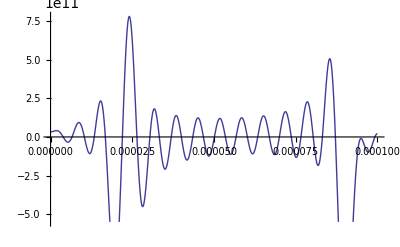

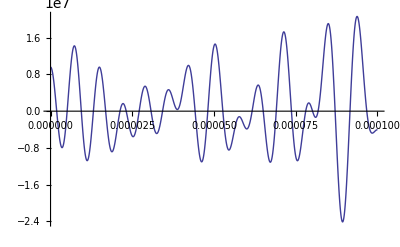

```mathematica
ClearAll["Global`*"]
(*Material parameters*)
chi = 4.07; (*electron affinity in eV*)
gamma = 5.47;  (*ionization energy in eV*)
phi = chi+gamma/2; (*work function in eV*)
Eg = gamma-chi;
ni = 2*10^6; (*intrinsic carrier concentration in [1/cm^3]*)
me = 9.1*10^-31; (*mass of electron  in kg*)
meffe = .067*me ;(*mass in density of states for electrons [1]*)
meffh = .47*me; (*mass in density of states for holes [1]*)
keV= 8.617*10^-5 ;(*boltzmann  constant in eV/K*)
ksi = 1.38*10^-23; (*boltzmann constant in J/K*)
T= 300; (*Cell temperature in K*)
h = 6.626 * 10^-34;
Ec = -chi;
Ev = -gamma;
e0m = 8.854*10^-12;  (*permittivity of free space in [s^4 A^2/m^3 kg]*)
e0 = e0m*10^-6; (*permittivity of free space in [s^4 A^2/cm^3 kg]*)
er =13.1; (*permittivity ratio for a given material [1]*)
q = 1.6*10^-19; (*Fundamental charge in C*)
taun=10^-9; (*electron lifetime in s*)
taup=10^-9;(*hole lifetime in s*)
mun =8500; (*electron mobility in cm^2/V s*)
mup = 400; (*hole mobility in cm^2/V s*)
Dn = 220; (*electron diffusivity in cm^2/s*)
Dp = 10; (*hole diffusivity in cm^2/s*)
Sr = 10^5; (*recombination velocity (in cm/s)*)
Wn = 10^-4; (*Lenght of n-type region (in cm)*)
Wp = 10^-4; (*Length of p-type region (in cm)*)

indexmax = 30;  (*The number of terms that will be included in the approximation*)
(*More terms corresponds to higher accuracy and longer runtimes*)
iterationsmax=2; (*Number of iterations used (higher brings closer to convergence*)

(*Determine basis functions for n-type carriers for later use*)
(*ONLY VALID IF BOUNDARY CONDITIONS ARE INEQUAL*)
(*Derived from boundary conditions*)
(*n'[0]=alp n[0]*)
(*n'[Wn]=beta n[Wn]*)

alpn = Sr/Dn;
betan = -(Sr/Dn); (*negative sign to account for opposing normal vectors at surface boundaries*)

Eq1n = Tan[mu*Wn]; 
Eq2n = ((alpn - betan)*mu)/(alpn*betan + mu^2); 
mucoeffn = mu; 

muansn = Table[FindRoot[Eq1n == Eq2n, {mu, (k*Pi)/Wn + 1/Wn}], {k, 0, indexmax+1}]; 
muoutn=Prepend[mucoeffn/.muansn,0];

muoutSinn = Prepend[mucoeffn /. muansn,0] ; (*Prepend a 0 for x=0 case*)
muoutCosn = Prepend[mucoeffn/. muansn, 0];  (*Prepend a 0 for x=0 case*)

sinesoutn = Table[Sin[muoutSinn[[index]]*x], {index, 1, indexmax+1}] ;
cosinesoutn = Table[Cos[muoutCosn[[index]]*x], {index, 1, indexmax+1 }];

(*Generate appropriate basis functions*)
(*Basis functions are scaled to ensure satisfaction of BCs*)
nbasis = Table[cosinesoutn[[index]]+alpn/muoutn[[index]] sinesoutn[[index]],{index,2,Length[sinesoutn]}];

(*Determine basis functions for p-type carriers for later use*)
(*ONLY VALID IF BOUNDARY CONDITIONS ARE INEQUAL*)
(*Derived from boundary conditions*)
(*n'[0]=alp n[0]*)
(*n'[Wn]=beta n[Wn]*)

alpp = Sr/Dp;
betap = -(Sr/Dp); (*negative sign to account for opposing normal vectors at surface boundaries*)

Eq1p = Tan[mu*Wn]; 
Eq2p = ((alpp - betap)*mu)/(alpp*betap + mu^2); 
mucoeffp = mu; 


muansp = Table[FindRoot[Eq1p == Eq2p, {mu, (k*Pi)/Wn + 3/(2Wn)}], {k, 0, indexmax+1}]; 
muoutp=Prepend[mucoeffp/.muansp,0];

muoutSinp = Prepend[mucoeffp /. muansp,0] ; (*Prepend a 0 for x=0 case*)
muoutCosp = Prepend[mucoeffp/. muansp, 0];  (*Prepend a 0 for x=0 case*)

sinesoutp= Table[Sin[muoutSinp[[index]]*x], {index, 1, indexmax+1}] ;
cosinesoutp = Table[Cos[muoutCosp[[index]]*x], {index, 1, indexmax+1 }];

(*Generate appropriate basis functions*)
(*Basis functions are scaled to ensure satisfaction of BCs*)
pbasis = Table[cosinesoutp[[index]]+alpp/muoutp[[index]] sinesoutp[[index]],{index,2,Length[sinesoutp]}];


(*Solar incidence data*)
alpha = 10000; (*/cm*) (*GaAs*)
Conc = 1;
Lflux = 2.0*10^17; (*/cm^2 s *) (*photons absorbed by GaAs at 1 sun*)
R=0.1; (*reflection coefficient*)
Gop = alpha*Conc*Lflux*(1-R)*Exp[-alpha*(x)];(*/cm^3*) 

(*Set up initial guess functions for carrier densities*)
p[x_]=Gop*taup;(*Initial guess for p[x]*) 
(*Nd + Gop as initial guess?*)
n[x_]= Gop*taun; (*Initial guess for n[x]*)

(*Swet up directories for storing output images*)
If[!DirectoryQ[NotebookDirectory[]<>"/pics/"<>ToString[indexmax]<>"terms"],
CreateDirectory[NotebookDirectory[]<>"/pics/"<>ToString[indexmax]<>"terms"]; (*Create a directory to store output plots*)
]


iterations=0; (*Reset temporary counter for while loop*)
While[iterations<iterationsmax,(*p[x] and n[x] change is significant*)
(*Store previous iterations of p[x] and n[x] to use at test for next iteration*)

(*Initialize coefficient array for n-type equation*)
nCoeff=Array[Coeffn,indexmax];

(*Calculate coefficients in n-type continuity equation*)
cn1 = Dn-ksi T mun/q;
cn2 = ksi T mun/q D[p[x],x]/p[x];
cn3 = ksi T mun/q(D[D[p[x],x],x]/p[x] - (D[p[x],x]/p[x])^2)-1/taun;


(*Set up left and side of equation*)
nLHS = Quiet[Table[NIntegrate[(cn1 D[D[nbasis[[jndex]],x],x]+cn2 D[nbasis[[jndex]],x]+cn3 nbasis[[jndex]])nbasis[[index]],{x,0,Wn}],{index,1,indexmax},{jndex,1,indexmax}]];

nLHS2 = Total[Transpose[Transpose[nLHS] nCoeff],{2}];

(*Set up right side of equation*)
nRHS = Quiet[Table[NIntegrate[-Gop nbasis[[index]],{x,0,Wn}],{index,1,indexmax}]];

(*Solve for coefficients*)
nSol = Solve[nLHS2==nRHS,nCoeff];

(*Reconstruct n[x]*)
n[x_]=Total[nbasis nCoeff/.nSol,2];

(*Print[n[Wn]];*)
(*Initialize coefficient array for p-type equation*)
pCoeff = Array[Coeffp,indexmax];

(*Calculate coefficients in p-type continuity equation*)
cp1 = ksi T mup/q - Dp;
cp2 = -ksi T mup/q D[n[x],x]/n[x];
cp3 = ksi T mup/q ((D[n[x],x]/n[x])^2- D[D[n[x],x],x]/n[x])-1/taup;

(*Set up left and side of equation*)
pLHS=Quiet[Table[NIntegrate[(cp1 D[D[pbasis[[jndex]],x],x] + cp2 D[pbasis[[jndex]],x] + cp3 pbasis[[jndex]])pbasis[[index]],{x,0,Wn}],{index,1,indexmax},{jndex,1,indexmax}]];

pLHS2 = Total[Transpose[Transpose[pLHS] pCoeff],{2}];

(*Set up right side of equation*)
pRHS = Quiet[Table[NIntegrate[-Gop pbasis[[index]], {x,0,Wn}],{index,1,indexmax}]];

(*Solve for coefficients*)
pSol = Solve[pLHS2==pRHS,pCoeff];

(*Reconstruct p[x]*)
p[x_] = Total[pbasis pCoeff/.pSol,2];

iterations++;(*Temporatry counter for For loop*)
Print[iterations];

(*Export outputs*)
Export[NotebookDirectory[]<>"/pics/"<>ToString[indexmax]<>"terms"<>"/iteration"<>ToString[iterations]<>"n.jpg",Plot[n[x],{x,0,Wn}]];
Export[NotebookDirectory[]<>"/pics/"<>ToString[indexmax]<>"terms"<>"/iteration"<>ToString[iterations]<>"p.jpg",Plot[p[x],{x,0,Wn}]];
]

Plot[Gop,{x,0,Wn}]

Plot[{n[x]},{x,0,Wn}]
Plot[{p[x]},{x,0,Wn}]
```

1.2136×10^12

1.21001×10^12

1.51641×10^12

7.92215×10^11

454.545

-454.545

10000.

-10000.

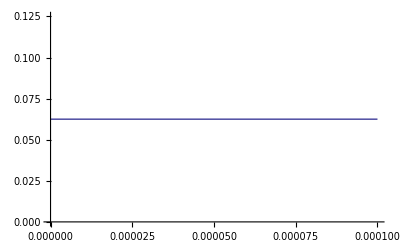

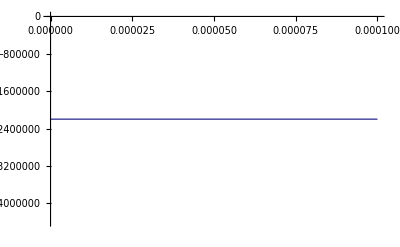

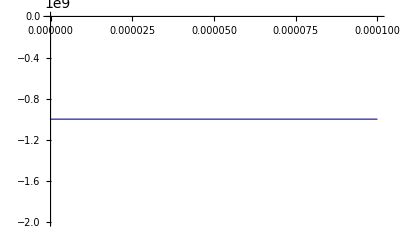

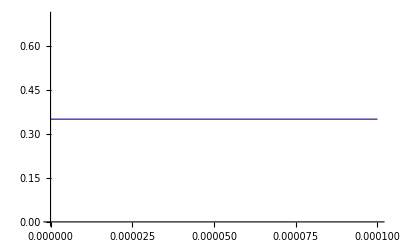

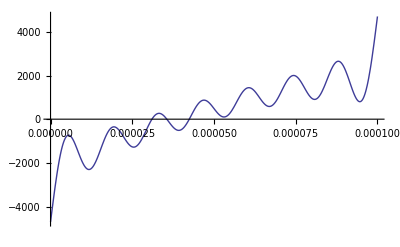

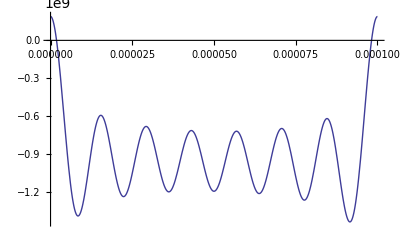

10.35

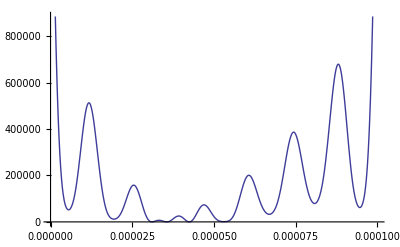

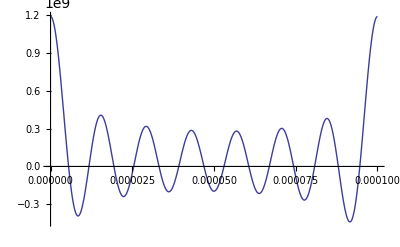

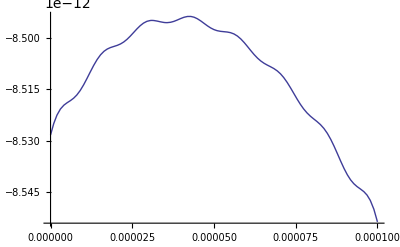

-Graphics-

-Graphics-

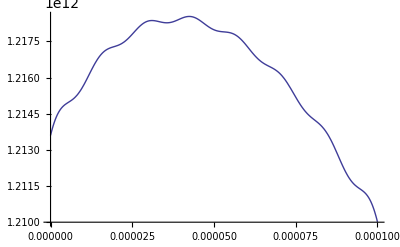

```mathematica
(*Endpoint checks*)
n[x]/.x->0
n[x]/.x->Wn
p[x]/.x->0
p[x]/.x->Wn

(*BC check*)
D[n[x],x]/n[x]/.x->0
D[n[x],x]/n[x]/.x->Wn
D[p[x],x]/p[x]/.x->0
D[p[x],x]/p[x]/.x->Wn



Plot[{cn1},{x,0,Wn}]
Plot[{cn2},{x,0,Wn}]
Plot[{cn3},{x,0,Wn}]
Plot[{cp1},{x,0,Wn}]
Plot[{cp2},{x,0,Wn}]
Plot[{cp3},{x,0,Wn}]

ksi T mup/q 
term1 = ksi T mup/q ((D[n[x],x]/n[x])^2);
Plot[term1,{x,0,Wn}]
term2=-ksi T mup/q (D[D[n[x],x],x]/n[x]);
Plot[term2,{x,0,Wn}]

term3=-ksi T mup/q (1/n[x]);
Plot[term3,{x,0,Wn}]

term4=-ksi T mup/q (D[D[n[x],x],x]);
Plot[{term4},{x,0,Wn}]
term5 = -ksi T mup/q  D[n[x],x];
Plot[{term5},{x,0,Wn}]
Plot[{n[x]},{x,0,Wn}]

cp3 = ksi T mup/q ((D[n[x],x]/n[x])^2- D[D[n[x],x],x]/n[x])-1/taup;
```